```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/systems/mul_helion_miwchan_M/results";
SetDirectory[workingdirectory];

matrixfilename="../LITstate/MATOUTB";
str=OpenRead[filename3,BinaryFormat->True];
headmarker=BinaryRead[str,"Integer32",ByteOrdering->$ByteOrdering];
NormHamMat=BinaryReadList[str,"Real64",ByteOrdering->$ByteOrdering];
JbasisDim=IntegerPart[Sqrt[Length[NormHamMat]*0.5]];
Close[str];
```

```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

Transpose::nmtx: The first two levels of If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{}],System`Dump`TextualCompact[{}]] cannot be transposed.

Set::shape: Lists If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{μs,Or}],System`Dump`TextualCompact[{μs,Or}]] and If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose[{}]],System`Dump`TextualCompact[Transpose[{}]]] are not the same shape.

Condition number ℕ_ij = 1.24689×10^7

EV_full(ℍ) = {10.6265,3.3563,2.27798,-6.2451}

EV_(EV (𝟙) > threshold)(ℍ) = {10.6265,3.3563,2.27798,-6.2451}

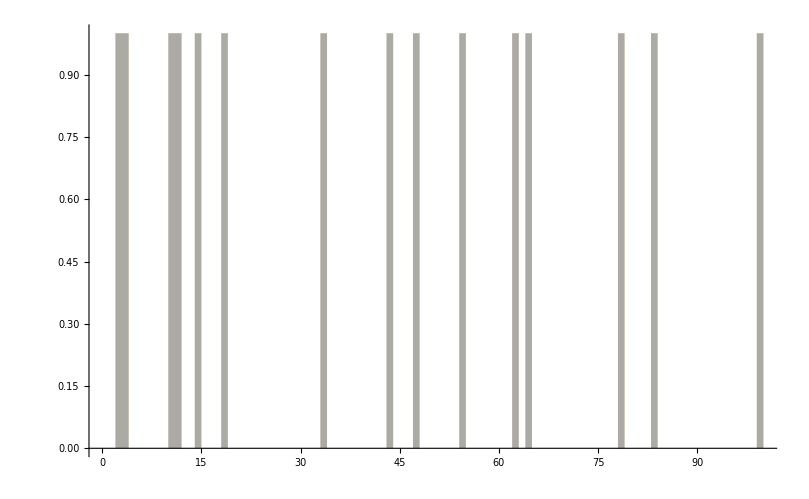

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;

thr=10^-13;

norm=ArrayReshape[NormHamMat[[1;;JbasisDim^2]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+1;;]],{JbasisDim,JbasisDim}];

decompose[thr,norm,ham];

evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evn=Eigenvalues[norm];

Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-4;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-4;;]]];

thh=100;(*Max[Abs[λs]];*)

Histogram[{Select[Re[evhamunnorm],Abs[#]<thh&],Re[Select[evhamnorm,Abs[#1]<thh&]]},{1},PlotRange->{{0,thh},Automatic}]
(*Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","ev(⟨α|H_nucl|β⟩) ev(𝟙) > "ScientificForm[thr]},{Sort[evn,Re[#1]>Re[#2]&]//MatrixForm,Sort[Eigenvalues[{ham,norm}],R~e[#1]>Re[#2]&]//MatrixForm,Sort[λs,Re[#1]>Re[#2]&]//MatrixForm}}]*)
```